# Cuestionario_02: Funciones elementales.

Sea

1. Introduce las funciones anteriores y haz el gráfico usando la función Plot. Utiliza un intervalo razonable para los valores de  x.

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);       g[x_]:=x;     h[x_]:=Sin[x/3] - Cos[x^3/5]
```

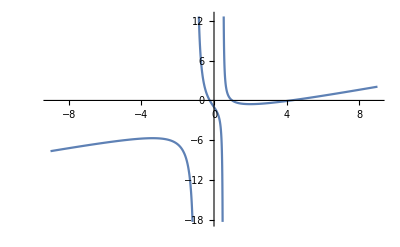

```mathematica
Plot[f[x],{x,-9,9}]
```

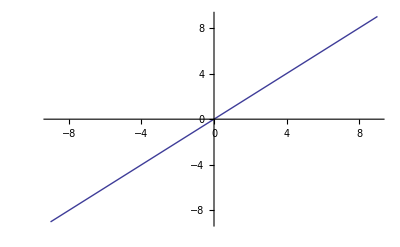

```mathematica
Plot[g[x],{x,-9,9}]
```

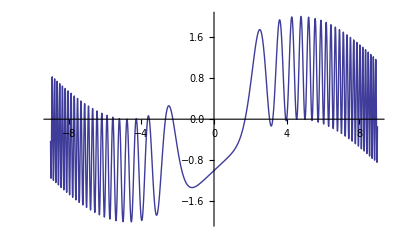

```mathematica
Plot[h[x],{x,-9,9}]
```

2 . g(x) es la bisectriz del primer-tercer cuadrante. Representa la gráfica de  f(x) y g(x) en el mismo gráfico. Hay tres puntos de corte entre ambas funciones. Obtén gráficamente las coordenadas (aproximadas) del punto de corte más lejano del origen de coordenadas.

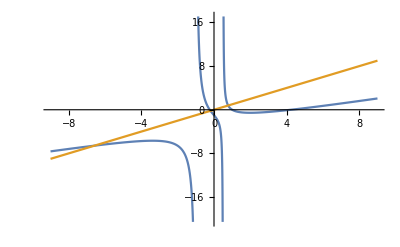

```mathematica
Plot[{f[x],g[x]},{x,-9,9}]
```

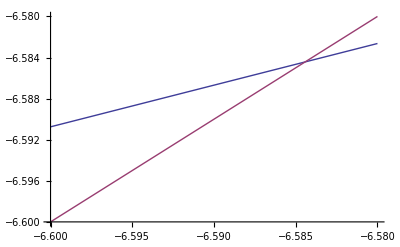

```mathematica
Plot[{f[x],g[x]},{x,-6.6,-6.58}]
```

Otro método. Este método es anecdótico y no se suele gastar:

```mathematica
AA= Plot[{f[x],g[x]},{x,-9,9}]
```

-Graphics-

```mathematica
{Graphics[AA,ImageSize->100],Dynamic[MousePosition["Graphics","Mouse not in graphics!"]]}
```

{-Graphics-,}

Por supuesto se puede resolver la ecuación numéricamente:

```mathematica
NSolve[f[x]==g[x],x]
```

{{x→-6.58443},{x→0.77931},{x→-0.194882}}

Coordenadas del punto x=   -6.585     , y=          -6.585

3. Calcula las asíntotas de f[x]

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);
```

```mathematica
Plot[f[x],{x,-9,9}]
```

-Graphics-

```mathematica
Solve[2 x^2+x-1==0,x]
```

{{x→-1},{x→1/2}}

Ahora puedes decir donde están las asíntotas verticales

```mathematica
asíntota vertical en {{x->-1},{x->1/2}}
```

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->1/2]
```

Indeterminate

Vamos a estudiar los límites laterales,  por la derecha

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->1/2,Direction->1]
```

-∞

límite por la izquierda

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->1/2,Direction->-1]
```

∞

las funciones racionales pueden tener una asíntota vertical en los puntos donde el denominador se hace cero (depende de sí la discontinuidad es evitable o no).

```mathematica
asíntota vertical en  {{x->-1},{x->1/2}}
```

```mathematica
Solve[x^3-5 x^2+3x+1==0,x]
```

{{x→1},{x→2-√5},{x→2+√5}}

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->+∞]
```

∞

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->-∞]
```

-∞

Para la asíntota oblicua utilizamos la fórmula del tutorial

```mathematica
m=Limit[((x^3-5 x^2+3x+1)/(2 x^2+x-1))/x,x->-∞]
```

1/2

```mathematica
n=Limit[((x^3-5 x^2+3x+1)/(2 x^2+x-1))-m x,x->-∞]
```

-11/4

```mathematica
AsyOb[x_]:=1/2 x -11/4
```

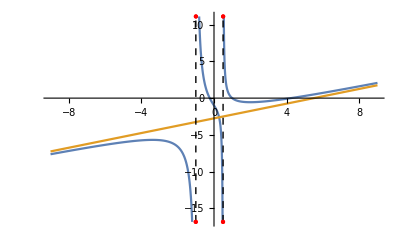

```mathematica
Plot[{     (x^3-5 x^2+3x+1)/(2 x^2+x-1),1/2 x -11/4},{x,-9,9},ExclusionsStyle->{Dashing[Small],Red}]
```

asíntota vertical:  x=-1       ; x=1/2
                                 asíntota oblicua: y=1/2 x -11/4

4. Determina las simetrías de las funciones  f(x), g(x) y h(x), calculando  f(-x), g(-x) y h(-x). Obtén como conclusión si la función es par, impar o ninguna de las dos.

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);       g[x_]:=x;     h[x_]:=Sin[x/3] - Cos[x^3/5]
```

```mathematica
f[-x]
```

(1-3 x-5 x^2-x^3)/(-1-x+2 x^2)

```mathematica
Simplify[f[x]-f[-x]]
```

(4 x (-2+5 x^2+x^4))/(1-5 x^2+4 x^4)

```mathematica
g[-x]
```

-x

```mathematica
Simplify[g[x]-g[-x]]
```

2 x

Si observas las gráficas puedes tener alguna duda respecto a las simetrías de h[x], pero puedes ver que no tienes simetrías con un contraejemplo, obtén el valor de la función en el punto x=3  y  x=-3 por ejemplo y verás que no tienes ningún tipo de simetrías.

```mathematica
N[h[3]]
```

0.206778

```mathematica
N[h[-3]]
```

-1.47616

```mathematica
h[-x]
```

-Cos[x^3/5]-Sin[x/3]

```mathematica
Simplify[h[x]-h[-x]]
```

2 Sin[x/3]

f(x) no tiene simetrías
                                     g(x) es    impar 
                                    h(x) no tiene simetrías